Last modified on: Tuesday, July 10, 2018 at 19:11

Author Info

Ian Fan

Sebastian Bodenstein

University of Melbourne

Poster Session Content

Reinforcement Q-Learning Agent

This project aims to create an Atari game agent using Q-Learning algorithm using Wolfram Language. The agent will not have any priori knowledge of the game and able to learn by self-play.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

Successfully implement classical q-learning agent on CartPole environment, able to achieve average performance of 195 episodes in 300 games. Tried to add time information in the input, the agent achieve 8k episodes within 300 games.

Make the Q-learning agent with multiple observation as input perform more stable and implement different techniques that increase the network’s performance like DDQN, Noisy net, etc.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

What is Reinforcement Learning

An area of Machine Learning, inspired by behaviourist psychology
Agent learn how to behave in a environment by performing actions and seeing the results.

Agent starts with state 0,
Agent chooses action A0,
Agent receives reward R0,
Agent goes to state 1, continue

-Graphics-

Value Network and Policy Network

In value-based RL, the input will be the current state or a combination of few recent states, and the output will be the estimated future reward of every possible action at this state. The goal will be to optimize the value function.

In policy-based RL, the input will be the current state or a combination of few recent states, and the output will be the most appropriate action at this state. The goal will be to optimize the policy function.

-Graphics--Graphics-

Deep Q Network

Give a state, the Q function predicts the total reward that it will received till the game is end of each action. The amazing part is that the Q function is predicting its own output. It uses a function to predict the result of iteratively evaluate every state.

-Graphics-

DQN in  CartPole

Here are there list animate shows the result of reinforcement learning on CartPole. The first is a random agent which does random action no matter the state. It’s average performance is around 23 episodes per game. The second agent is the result of classical DQN agent which only takes current observation as input, its average performance is around 3000. The third agent is also DQN agent but takes the current observation and previous observation as input, it has a performance of 8000 and peak performance actually reaches 10,000 which is the limit I set for this game.

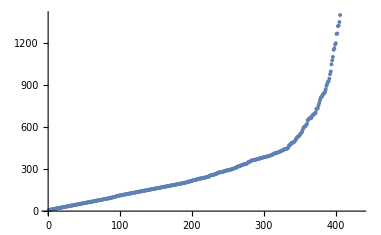

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

solve the CarPole environment within 300 games
Develop an agent able to reach over 8000 average performance in CartPole environment

#### Code

Provide one of:

https://github.com/ianfanx/wss2018Project

#### Written Content / Lesson Plans

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

https://medium.freecodecamp.org/an-introduction-to-reinforcement-learning-4339519de419

#### Future Directions

Increase the stability of the current method (take in multiple observation as input)
Let the agent play on Pong
Combine value network with different technique including DDQN, A3C, Noisy Net, etc and implement Rainbow algorithm

#### Background Info Links/References

https://www.cs.toronto.edu/~vmnih/docs/dqn.pdf
https://gym.openai.com/

#### Keywords

Provide keywords as items

Reinforcement Learning

Deep Q Network

#### Other information